1. Naravna in cela števila:
17) Babica je vnučki za nakup kolesa dala 17 evrov, dedek pa trikrat toliko. Ker stane kolo 112 evrov, bo morala ostalo dodati mama. Koliko denarja bo prispevala mama?

```mathematica
Solve[17 + (3 * 17) +x == 112, x]
```

{{x→44}}

Mama bo prispevala 44 evrov.

2. Potence:
5) Izračunaj:

a)

```mathematica
(-6)^3 + (-4)^3 * ((-5)^2-(-1)^5 * (-3)^3)
```

-88

b)

```mathematica
(-3)^4* (-2) - (-1)^19 * ((-7)^2 - 2 * (-4)^2)
```

-145

c)

```mathematica
5^2 * (-2)^2- (-3)^2 * ((-6)^2 + (-1)^4 * (-2)^5)
```

64

d)

```mathematica
((-2)^3 + (-5)^2) * (-1)^3 - ((-3)^2 * (-2) - (-4)^2)
```

17

e)

```mathematica
(-3)^2 * (-1)^7- 4^2* ((-3)^3 * (-2)^2-2^4 * (-3) * (-1)^6)
```

951

f)

```mathematica
(-8)^2 * (-1)^11 - (-3)^2* (4 * (-3)^3 + (-2)^2 * (-5)^2 - (-1)^7 * (-2)^3)
```

80

3. Računanje z izrazi:
4) Zmnoži polinoma:

a)

```mathematica
Expand[(2x+1) * (x -3)]
```

-3-5 x+2 x^2

b)

```mathematica
Expand[(3x-2)*(x+4)]
```

-8+10 x+3 x^2

c)

```mathematica
Expand[(4x+3)*(2x-5)]
```

-15-14 x+8 x^2

d)

```mathematica
Expand[(6x+11)*(2x-7)]
```

-77-20 x+12 x^2

e)

```mathematica
Expand[(2x+7)*(3x+1)]
```

7+23 x+6 x^2

f)

```mathematica
Expand[(5x-1)*(4x-9)]
```

9-49 x+20 x^2

4. Racionalna števila:
6) Izračunaj:

a)

```mathematica
((8+3/4)-(7+1/2))*(5+1/3+1+3/5)
```

26/3

b)

```mathematica
((1+16/19)/(5/19))/((2+1/10)/(1+2/3))
```

50/9

c)

```mathematica
(2+2/5)*(1+1/4-1/3)-(1-5/8)/(5/6)
```

7/4

d)

```mathematica
((2+1/12)*3/5-3/7)/(3+1/4-2)
```

23/35

5. Decimalna števila:
12) Izračunaj:

a)

```mathematica
Rationalize[(8/11 + 1.8)/(71/30- (1+5/6))]
```

417/88

b)

```mathematica
Rationalize[(26/15-1.5^-1)/(7/5-49/75)]
```

10/7

c)

```mathematica
Rationalize[(9/11)/(36/55)-(4+5/7)*7/18]
```

-7/12

d)

```mathematica
Rationalize[(79/15+(2+1/5))/(4.25 - 3/11)]
```

704/375

Opomba: periode sem pretvarjal v ulomke s pomočjo funkcije Rationalize, primer:

```mathematica
Rationalize[0.272727272727272727]
```

3/11

6. Realna števila:
11) Izračunaj:

a)

```mathematica
Abs[((-8)*Abs[-9]-Abs[-27])*7-Abs[-5]*(Abs[14]-(-19))]
```

858

b)

```mathematica
Abs[-8*(Abs[-6]*(-9)-Abs[-23])-Abs[-4]*(Abs[-7]-(-19))]
```

512

c)

```mathematica
Abs[-7*(Abs[-8]*(-6)-Abs[-18])-Abs[-9]*(Abs[-5]-(-19))]
```

246

d)

```mathematica
Abs[-3*(Abs[-4]-(Abs[-5]*(-2)-Abs[-6]))-7*Abs[-(-20)-4*Abs[-2-(-8)]]]
```

88

Opomba: uradne rešitve so napačne.

7. Linearna enačba:
6) Reši enačbo:

a)

```mathematica
Solve[(3x-2)/4-(2x-1)/2==(4x+3)/8]
```

{{x→-1/2}}

b)

```mathematica
Solve[(7x+1)/5-(3x+2)/3==x-(4x+9)/15]
```

{{x→2/5}}

c)

```mathematica
Solve[(2x-5)/6-(5x-3)/4==2-(9-4x)/8]
```

{{x→-23/34}}

d)

```mathematica
Solve[(2x-5)/9-(3x-7)/6==(8x+1)/3-(5x-2)/4]
```

{{x→-8/61}}

e)

```mathematica
Solve[(4x+3)/2-(3x-5)/4==(3x-8)/6-(7x)/12]
```

{{x→-49/16}}

f)

```mathematica
Solve[(5x+2)/4-(8x+1)/9==(7x+3)/6-(4x-2)/3]
```

{{x→28/19}}

8. Kotne funkcije v pravokotnem trikotniku:
3) Izračunaj vrednost kotne funkcije:

a)

```mathematica
Sin[28.32°]
```

0.474396

b)

```mathematica
Cos[83.142°]
```

0.119409

c)

```mathematica
Tan[65.5493°]
```

2.19931

d)

```mathematica
Sin[84.2157°]
```

0.994908

e)

```mathematica
Cos[39.8974°]
```

0.767194

f)

```mathematica
Cot[41.329°]
```

1.13711

9. Računanje s koreni:
2) Izračunaj:

a)

```mathematica
√2*√18
```

6

b)

```mathematica
√(2*7*7*8)
```

28

c)

```mathematica
√13*√52
```

26

d)

```mathematica
√(1+1/5)*√(5/24)
```

1/2

e)

```mathematica
√3*√27
```

9

f)

```mathematica
√(4*10^6)
```

2000

g)

```mathematica
√8*√72
```

24

h)

```mathematica
√(2+1/5)*√(11+4/11)
```

5

10. Kotne funkcije:
19) Nariši grafe kotnih funkcij:

a)

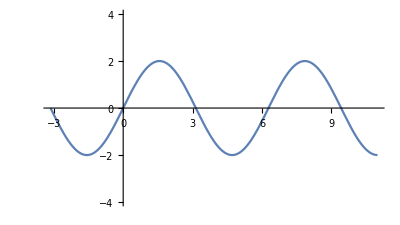

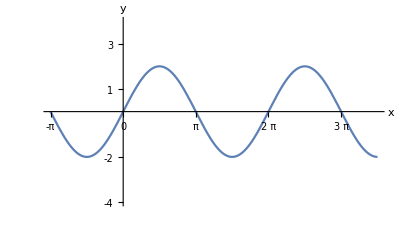

```mathematica
slika1 = Plot[2*Sin[x], {x, -π, 3.5π},AspectRatio->Automatic,PlotRange->{-4,4}]
Show[slika1,Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi, (3Pi)/2, 2Pi, (5Pi)/2, 3Pi}, {-4, -3, -2, -1, 1, 2, 3, 4}}, AxesLabel->{"x","y"}]
```

b)

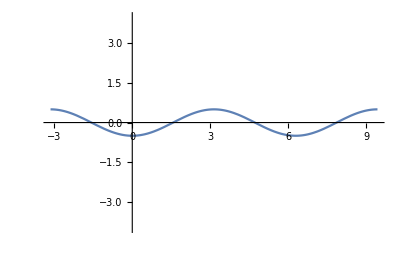

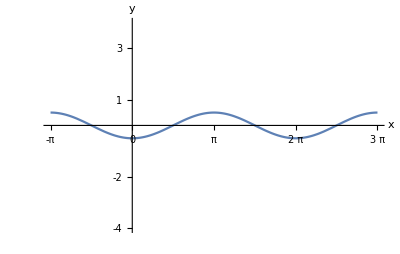

```mathematica
slika2 = Plot[-1/2*Cos[x], {x, -π, 3π},AspectRatio->Automatic,PlotRange->{-4,4}]
Show[slika2,Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi, (3Pi)/2, 2Pi, (5Pi)/2, 3Pi}, {-4, -3, -2, -1, 1, 2, 3, 4}}, AxesLabel->{"x","y"}]
```

c)

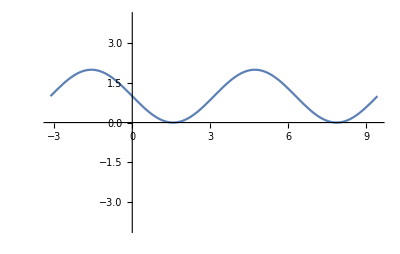

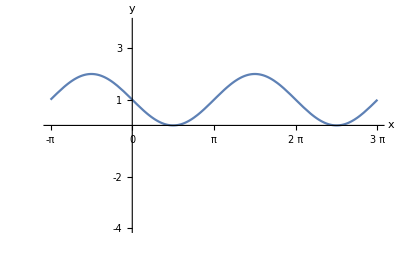

```mathematica
slika3 = Plot[-Sin[x]+1, {x, -π, 3π},AspectRatio->Automatic,PlotRange->{-4,4}]
Show[slika3,Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi, (3Pi)/2, 2Pi, (5Pi)/2, 3Pi}, {-4, -3, -2, -1, 1, 2, 3, 4}}, AxesLabel->{"x","y"}]
```

d)

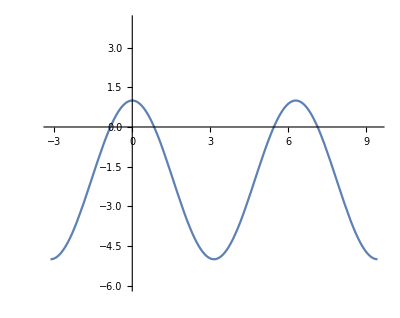

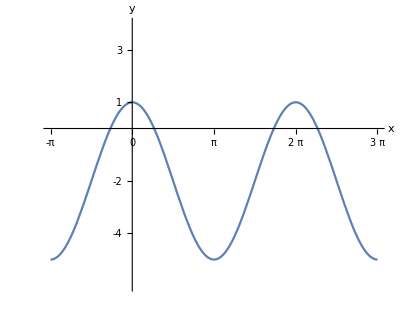

```mathematica
slika4 = Plot[3*Cos[x]-2, {x, -π, 3π},AspectRatio->Automatic,PlotRange->{-6,4}]
Show[slika4,Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi, (3Pi)/2, 2Pi, (5Pi)/2, 3Pi}, {-4, -3, -2, -1, 1, 2, 3, 4}}, AxesLabel->{"x","y"}]
```